```mathematica
Clear["Global`*"];
```

```mathematica
path="/home/sepand/Downloads/test/";
a=ReadList[path<>"add_glo_kernel", Number];
b=ReadList[path<>"add_loc_kernel", Number];
```

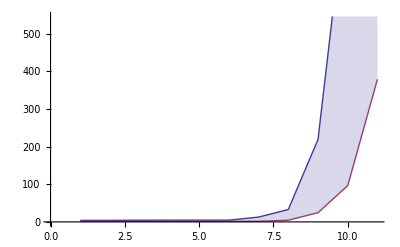

```mathematica
ListLinePlot[{a,b},Filling->Axis(*{1->{2}}*)]
```